# Historical Daily Closing Prices

## Supplemental material for Secs. 7.9 and 7.10.

## Setup

### Durations

```mathematica
month={"2025-01-01","2025-01-31"};
year={"2025-01-01","2025-12-31"};
decade={"2015-01-01","2025-12-31"};
```

### Dates

```mathematica
minute=60;
hour=60minute;
day=24hour;
```

### Export Directory

```mathematica
exportDirectory=NotebookDirectory[]<>"/output/financialData";
```

```mathematica
SetDirectory@exportDirectory
```

## Brownian Motion in Log-Price

```mathematica
posteriorAction[x_,t_,σ_,μ_]:=Block[{n},
n=Length@x;
If[Length@t!=n,Print["Error: x and t have different lengths"]];
Sum[
1/(2 σ^2(t[[i+1]]-t[[i]]))(x[[i+1]]-x[[i]]-μ(t[[i+1]]-t[[i]]))^2
,{i,1,n-1}]
+n Log[σ] (* Normalization plus Jeffreys prior *)
]
```

#### Symbolic Example

```mathematica
posteriorAction[{x1,x2,x3},{t1,t2,t3},σ,μ]
```

(-x1+x2-(-t1+t2) μ)^2/(2 (-t1+t2) σ^2)+(-x2+x3-(-t2+t3) μ)^2/(2 (-t2+t3) σ^2)+3 Log[σ]

```mathematica
Exp[-posteriorAction[{0,x},{0,t},σ,μ]]
```

(ⅇ^(-(x-t μ)^2/(2 t σ^2)))/σ^2

```mathematica
Integrate[Exp[-posteriorAction[{0,x},{0,t},σ,μ]],{x,-∞,∞},Assumptions->σ>0&&t>0]
```

(√(2 π) √t)/σ

The overall 1/σ is the Jeffreys prior. The overall ∏ _(i=1)^(N-1) 1/(2π  Δt_i)^(1/2) is not relevant for determination of the maximum, so I dropped it.

### Uncertainty matrix

```mathematica
Mσσ[x_,t_,σ_,μ_]:=D[posteriorAction[x,t,σ,μ], σ,σ]
```

```mathematica
Mμμ[x_,t_,σ_,μ_]:=D[posteriorAction[x,t,σ,μ], μ,μ]
```

```mathematica
Mσμ[x_,t_,σ_,μ_]:=D[posteriorAction[x,t,σ,μ], σ,μ]
```

## Financial Data

```mathematica
?FinancialData
```

Jan. 9 was a national day of mourning for the passing of former president Carter. The markets were closed. 20 data points is correct for Jan 2025.

### Stocks

```mathematica
stocks={"AAPL","NVDA","GLD","SLV","USO","UNG","SOYB"};
```

### Daily Closing Prices over 1 Month

```mathematica
FinancialData["AAPL"]
```

259.48 $

```mathematica
dailyClosingPricesMonth=FinancialData[stocks,month]
```

{TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…]}

In January, 2025, there were 23 weekdays and 3 holidays: New Year’s Day, Martin Luther King Jr. Day, and, for that year specifically, Jan. 9, when the markets were closed for the death of President Carter. The total number of daily closing prices should therefore be 20.

REMARK: Sometimes, for reasons beyond the ken of mortal men, the above call to FinancialData[] claims to return only 18 data points. If that happens, call FinancialData[] with different arguments, like FinancialData[“AAPL”], then try again. Wolfram, once again, knocks it out of the park on quality control.

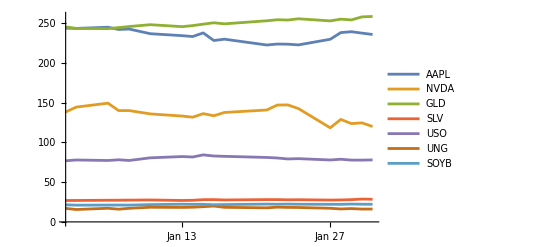

```mathematica
ListLinePlot[dailyClosingPricesMonth,PlotLegends->stocks]
```

```mathematica
LogPriceFromPrice[timeSeries_]:=Log[#/(#[[1]])]&/@Comap[QuantityMagnitude@timeSeries,"Values"]
```

```mathematica
logDailyClosingPricesMonth=LogPriceFromPrice@dailyClosingPricesMonth;
```

```mathematica
LogPricePlot[logPrices_,plotLabel_]:=ListLinePlot[logPrices,
PlotLegends->stocks,
Frame->{{True,False},{True,False}},
FrameLabel->{"day","log-price"},
LabelStyle->Directive[Black,12],
PlotLabel->plotLabel,
PlotRange->All,
PlotStyle->{
RGBColor[0.8,0,0],RGBColor[0,0.8,0],RGBColor[0.88,0.67,0],
RGBColor[0.7,0.7,0.7],RGBColor[0,0,0],RGBColor[0,0.7,0.7],
RGBColor[0.8,0.6,0.8]}]
```

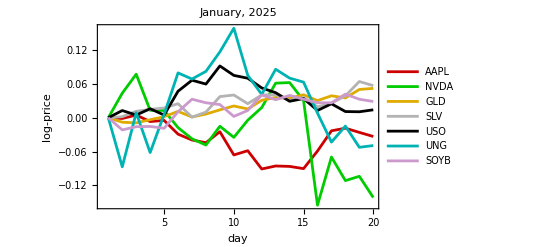

```mathematica
logPricePlotMonth=LogPricePlot[logDailyClosingPricesMonth,"January, 2025"]
```

```mathematica
Export["logPriceMonth.pdf",logPricePlotMonth]
```

logPriceMonth.pdf

#### Dates

```mathematica
DatesFromPrice[timeSeries_]:=(#-#[[1]])/day&/@Comap[timeSeries,"Times"]
```

```mathematica
dailyClosingPricesDatesMonth=DatesFromPrice@dailyClosingPricesMonth
```

{{0,1,4,5,6,8,11,12,13,14,15,19,20,21,22,25,26,27,28,29},{0,1,4,5,6,8,11,12,13,14,15,19,20,21,22,25,26,27,28,29},{0,1,4,5,6,8,11,12,13,14,15,19,20,21,22,25,26,27,28,29},{0,1,4,5,6,8,11,12,13,14,15,19,20,21,22,25,26,27,28,29},{0,1,4,5,6,8,11,12,13,14,15,19,20,21,22,25,26,27,28,29},{0,1,4,5,6,8,11,12,13,14,15,19,20,21,22,25,26,27,28,29},{0,1,4,5,6,8,11,12,13,14,15,19,20,21,22,25,26,27,28,29}}

```mathematica
Length/@dailyClosingPricesDatesMonth
```

{20,20,20,20,20,20,20}

It is important, but not a problem, that the times are not equally spaced.

### Year

```mathematica
stocks
```

{AAPL,NVDA,GLD,SLV,USO,UNG,SOYB}

```mathematica
dailyClosingPricesYear=FinancialData[stocks,year]
```

{TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…]}

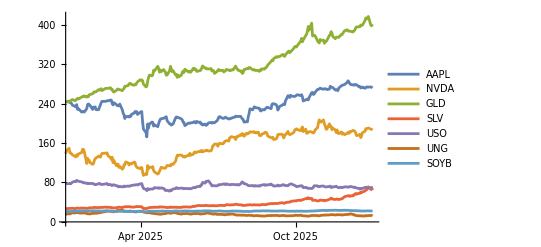

```mathematica
ListLinePlot[dailyClosingPricesYear,PlotLegends->stocks]
```

```mathematica
logDailyClosingPricesYear=LogPriceFromPrice@dailyClosingPricesYear;
```

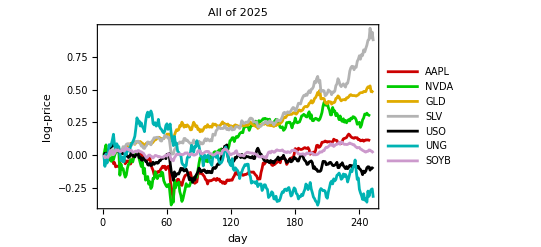

```mathematica
logPricePlotYear=LogPricePlot[logDailyClosingPricesYear,"All of 2025"]
```

```mathematica
Export["logPriceYear.pdf",logPricePlotYear]
```

logPriceYear.pdf

#### Dates

```mathematica
dailyClosingPricesDatesYear=DatesFromPrice@dailyClosingPricesYear;
```

### Decade

```mathematica
dailyClosingPricesDecade=FinancialData[stocks,decade]
```

{TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…]}

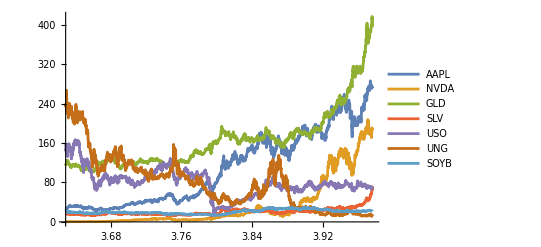

```mathematica
ListLinePlot[dailyClosingPricesDecade,PlotLegends->stocks]
```

```mathematica
logDailyClosingPricesDecade=LogPriceFromPrice@dailyClosingPricesDecade;
```

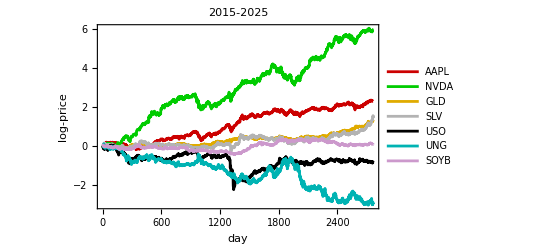

```mathematica
logPricePlotDecade=LogPricePlot[logDailyClosingPricesDecade,"2015-2025"]
```

```mathematica
Export["logPriceDecade.pdf",logPricePlotDecade]
```

logPriceDecade.pdf

#### Dates

```mathematica
dailyClosingPricesDatesDecade=DatesFromPrice@dailyClosingPricesDecade;
```

## Inference

### Month

```mathematica
posteriorActionMonth[σ_,μ_]=Table[
posteriorAction[#1,#2,σ,μ]&[logDailyClosingPricesMonth[[i]],dailyClosingPricesDatesMonth[[i]]],
{i,1,Length@stocks}];
```

```mathematica
estimatesMonth=Table[
NMinimize[{posteriorActionMonth[σ,μ][[i]],σ>0},{σ,μ}][[2]],
{i,1,Length@stocks}]
```

{{σ→0.0152567,μ→-0.00114733},{σ→0.0411995,μ→-0.00488555},{σ→0.00611249,μ→0.00179851},{σ→0.0110229,μ→0.001966},{σ→0.013663,μ→0.000485146},{σ→0.0455702,μ→-0.00170371},{σ→0.0108909,μ→0.000994535}}

```mathematica
ΔtMaxMonth=Table[
Max[Differences@dailyClosingPricesDatesMonth[[i]]],
{i,1,Length@stocks}]
```

{4,4,4,4,4,4,4}

```mathematica
(σ/.estimatesMonth)*ΔtMaxMonth
```

{0.0610269,0.164798,0.02445,0.0440918,0.054652,0.182281,0.0435635}

#### Uncertainty matrix

```mathematica
uncertaintiesMonth=
Table[
{
{Mσσ[#1,#2,σ,μ],Mσμ[#1,#2,σ,μ]},
{Mσμ[#1,#2,σ,μ],Mμμ[#1,#2,σ,μ]}
}/.estimatesMonth[[i]]&
[logDailyClosingPricesMonth[[i]],dailyClosingPricesDatesMonth[[i]]]//Chop,
{i,1,Length@stocks}
]
```

{{{171845.,0},{0,124588.}},{{23565.4,0},{0,17084.9}},{{1.07059×10^6,0},{0,776179.}},{{329204.,0},{0,238673.}},{{214273.,0},{0,155348.}},{{19261.8,0},{0,13964.8}},{{337236.,0},{0,244496.}}}

```mathematica
uncertaintiesMonth//MatrixForm
```

((171845.
0) | (0
124588.)
(23565.4
0) | (0
17084.9)
(1.07059×10^6
0) | (0
776179.)
(329204.
0) | (0
238673.)
(214273.
0) | (0
155348.)
(19261.8
0) | (0
13964.8)
(337236.
0) | (0
244496.))

They are diagonal, as they should be.

```mathematica
Eigensystem/@uncertaintiesMonth//Chop//MatrixForm
```

((171845.
124588.) | ({-1.,0}
{0,-1.})
(23565.4
17084.9) | ({-1.,0}
{0,-1.})
(1.07059×10^6
776179.) | ({-1.,0}
{0,-1.})
(329204.
238673.) | ({-1.,0}
{0,-1.})
(214273.
155348.) | ({-1.,0}
{0,-1.})
(19261.8
13964.8) | ({-1.,0}
{0,-1.})
(337236.
244496.) | ({-1.,0}
{0,-1.}))

```mathematica
uncertaintiesMonthEigenvalues=Eigenvalues/@uncertaintiesMonth
```

{{171845.,124588.},{23565.4,17084.9},{1.07059×10^6,776179.},{329204.,238673.},{214273.,155348.},{19261.8,13964.8},{337236.,244496.}}

```mathematica
uncertaintyInVolatilityMonth=Table[
(1/(uncertaintiesMonthEigenvalues[[i]][[1]]))^(1/2),
{i,1,Length@stocks}]
```

{0.0024123,0.00651422,0.000966469,0.00174288,0.00216031,0.00720529,0.001722}

```mathematica
uncertaintyInDriftMonth=Table[
(1/(uncertaintiesMonthEigenvalues[[i]][[2]]))^(1/2),
{i,1,Length@stocks}]
```

{0.0028331,0.00765056,0.00113506,0.00204691,0.00253716,0.00846218,0.00202239}

#### Results

```mathematica
Print["*******************************"];
Print["Inferences from a month of data"];
Print["*******************************"];
Table[
Print[stocks[[i]],":"];
Print["  σ = ",ScientificForm[σ/.estimatesMonth[[i]],2]," ± ",ScientificForm[uncertaintyInVolatilityMonth[[i]],2]," day^(-1/2)"];
Print["  μ = ",ScientificForm[μ/.estimatesMonth[[i]],2]," ± ",ScientificForm[uncertaintyInDriftMonth[[i]],2]," day^-1"],
{i,1,Length@stocks}
];
```

*******************************

Inferences from a month of data

*******************************

AAPL:

σ = 1.5×10^-2 ± 2.4×10^-3 day^(-1/2)

μ = -1.1×10^-3 ± 2.8×10^-3 day^-1

NVDA:

σ = 4.1×10^-2 ± 6.5×10^-3 day^(-1/2)

μ = -4.9×10^-3 ± 7.7×10^-3 day^-1

GLD:

σ = 6.1×10^-3 ± 9.7×10^-4 day^(-1/2)

μ = 1.8×10^-3 ± 1.1×10^-3 day^-1

SLV:

σ = 1.1×10^-2 ± 1.7×10^-3 day^(-1/2)

μ = 2.×10^-3 ± 2.×10^-3 day^-1

USO:

σ = 1.4×10^-2 ± 2.2×10^-3 day^(-1/2)

μ = 4.9×10^-4 ± 2.5×10^-3 day^-1

UNG:

σ = 4.6×10^-2 ± 7.2×10^-3 day^(-1/2)

μ = -1.7×10^-3 ± 8.5×10^-3 day^-1

SOYB:

σ = 1.1×10^-2 ± 1.7×10^-3 day^(-1/2)

μ = 9.9×10^-4 ± 2.×10^-3 day^-1

It is conventional to multiply the results by the appropriate power of

```mathematica
numberOfTradingDaysPerYear=252; (* This is approximate, or an average, because of days like Jan. 9, 2025. *)
```

and to quote the results in percentages:

```mathematica
Print["**********************************************"];
Print["Inferences from a month of data (standardized)"];
Print["**********************************************"];
Table[
Print[stocks[[i]],":"];
Print["  σ = ",SetPrecision[(σ/.estimatesMonth[[i]])Sqrt[numberOfTradingDaysPerYear]*100,2]," ± ",SetPrecision[(uncertaintyInVolatilityMonth[[i]])Sqrt[numberOfTradingDaysPerYear]*100,2]," %/year^(1/2)"];
Print["  μ = ",SetPrecision[(μ/.estimatesMonth[[i]])numberOfTradingDaysPerYear*100,2]," ± ",SetPrecision[(uncertaintyInDriftMonth[[i]])numberOfTradingDaysPerYear*100,2]," %/year"],
{i,1,Length@stocks}
];
```

**********************************************

Inferences from a month of data (standardized)

**********************************************

AAPL:

σ = 24. ± 3.8 %/year^(1/2)

μ = -29. ± 71. %/year

NVDA:

σ = 65. ± 10. %/year^(1/2)

μ = -120. ± 190. %/year

GLD:

σ = 9.7 ± 1.5 %/year^(1/2)

μ = 45. ± 29. %/year

SLV:

σ = 17. ± 2.8 %/year^(1/2)

μ = 50. ± 52. %/year

USO:

σ = 22. ± 3.4 %/year^(1/2)

μ = 12. ± 64. %/year

UNG:

σ = 72. ± 11. %/year^(1/2)

μ = -43. ± 210. %/year

SOYB:

σ = 17. ± 2.7 %/year^(1/2)

μ = 25. ± 51. %/year

### Year

```mathematica
posteriorActionYear[σ,μ]=Table[
posteriorAction[logDailyClosingPricesYear[[i]],dailyClosingPricesDatesYear[[i]],σ,μ],
{i,1,Length@stocks}];
```

```mathematica
estimatesYear=Table[
NMinimize[{posteriorActionYear[σ,μ][[i]],σ>0},{σ,μ}][[2]],
{i,1,Length@stocks}]
```

{{σ→0.0186459,μ→0.000299542},{σ→0.0280017,μ→0.000823509},{σ→0.0107063,μ→0.00132018},{σ→0.0181714,μ→0.00240271},{σ→0.0175142,μ→-0.000293315},{σ→0.0313261,μ→-0.000902092},{σ→0.00811453,μ→0.000041904}}

```mathematica
ΔtMaxYear=Table[
Max[Differences@dailyClosingPricesDatesYear[[i]]],
{i,1,Length@stocks}]
```

{4,4,4,4,4,4,4}

```mathematica
(σ/.estimatesYear)*ΔtMaxYear
```

{0.0745836,0.112007,0.042825,0.0726855,0.0700567,0.125304,0.0324581}

#### Uncertainty matrix

```mathematica
uncertaintiesYear=Table[
{
{Mσσ[#1,#2,σ,μ],Mσμ[#1,#2,σ,μ]},
{Mσμ[#1,#2,σ,μ],Mμμ[#1,#2,σ,μ]}
}/.estimatesYear[[i]]&[logDailyClosingPricesYear[[i]],dailyClosingPricesDatesYear[[i]]]//Chop,
{i,1,Length@stocks}
]
```

{{{1.43815×10^6,0},{0,1.04409×10^6}},{{637676.,1.74623×10^-10},{1.74623×10^-10,462953.}},{{4.41444×10^6,9.31323×10^-10},{9.31323×10^-10,3.16688×10^6}},{{1.53241×10^6,0},{0,1.09934×10^6}},{{1.64957×10^6,0},{0,1.18339×10^6}},{{515630.,0},{0,369909.}},{{7.68464×10^6,-2.32831×10^-10},{-2.32831×10^-10,5.5129×10^6}}}

That should be exactly diagonal, but maybe there is a problem of numerical precision.

```mathematica
uncertaintiesYearEigenvalues=Eigenvalues/@uncertaintiesYear//Chop
```

{{1.43815×10^6,1.04409×10^6},{637676.,462953.},{4.41444×10^6,3.16688×10^6},{1.53241×10^6,1.09934×10^6},{1.64957×10^6,1.18339×10^6},{515630.,369909.},{7.68464×10^6,5.5129×10^6}}

```mathematica
uncertaintyInVolatilityYear=Table[
(1/(uncertaintiesYearEigenvalues[[i]][[1]]))^(1/2),
{i,1,Length@stocks}
]
```

{0.00083387,0.00125228,0.000475951,0.000807816,0.0007786,0.00139261,0.000360735}

```mathematica
uncertaintyInDriftYear=Table[
(1/(uncertaintiesYearEigenvalues[[i]][[2]]))^(1/2),
{i,1,Length@stocks}
]
```

{0.000978656,0.00146971,0.000561932,0.00095375,0.000919256,0.00164419,0.000425902}

The volatility estimate has gotten more reliable; the drift estimate remains swamped by uncertainty.

#### Results

```mathematica
Print["******************************"];
Print["Inferences from a year of data"];
Print["******************************"];
Table[
Print[stocks[[i]],":"];
Print["  σ = ",ScientificForm[σ/.estimatesYear[[i]],2]," ± ",ScientificForm[uncertaintyInVolatilityYear[[i]],2]," day^(-1/2)"];
Print["  μ = ",ScientificForm[μ/.estimatesYear[[i]],2]," ± ",ScientificForm[uncertaintyInDriftYear[[i]],2]," day^-1"],
{i,1,Length@stocks}
];
```

******************************

Inferences from a year of data

******************************

AAPL:

σ = 1.9×10^-2 ± 8.3×10^-4 day^(-1/2)

μ = 3.×10^-4 ± 9.8×10^-4 day^-1

NVDA:

σ = 2.8×10^-2 ± 1.3×10^-3 day^(-1/2)

μ = 8.2×10^-4 ± 1.5×10^-3 day^-1

GLD:

σ = 1.1×10^-2 ± 4.8×10^-4 day^(-1/2)

μ = 1.3×10^-3 ± 5.6×10^-4 day^-1

SLV:

σ = 1.8×10^-2 ± 8.1×10^-4 day^(-1/2)

μ = 2.4×10^-3 ± 9.5×10^-4 day^-1

USO:

σ = 1.8×10^-2 ± 7.8×10^-4 day^(-1/2)

μ = -2.9×10^-4 ± 9.2×10^-4 day^-1

UNG:

σ = 3.1×10^-2 ± 1.4×10^-3 day^(-1/2)

μ = -9.×10^-4 ± 1.6×10^-3 day^-1

SOYB:

σ = 8.1×10^-3 ± 3.6×10^-4 day^(-1/2)

μ = 4.2×10^-5 ± 4.3×10^-4 day^-1

(Note that the units are still in days: Whether I use a month, a year, or a decade of daily closing prices, they are still daily closing prices.)

```mathematica
Print["*********************************************"];
Print["Inferences from a year of data (standardized)"];
Print["*********************************************"];
Table[
Print[stocks[[i]],":"];
Print["  σ = ",SetPrecision[(σ/.estimatesYear[[i]])Sqrt[numberOfTradingDaysPerYear]*100,2]," ± ",SetPrecision[(uncertaintyInVolatilityYear[[i]])Sqrt[numberOfTradingDaysPerYear]*100,2]," %/year^(1/2)"];
Print["  μ = ",SetPrecision[(μ/.estimatesYear[[i]])numberOfTradingDaysPerYear*100,2]," ± ",SetPrecision[(uncertaintyInDriftYear[[i]])numberOfTradingDaysPerYear*100,2]," %/year"],
{i,1,Length@stocks}
];
```

*********************************************

Inferences from a year of data (standardized)

*********************************************

AAPL:

σ = 30. ± 1.3 %/year^(1/2)

μ = 7.5 ± 25. %/year

NVDA:

σ = 44. ± 2. %/year^(1/2)

μ = 21. ± 37. %/year

GLD:

σ = 17. ± 0.76 %/year^(1/2)

μ = 33. ± 14. %/year

SLV:

σ = 29. ± 1.3 %/year^(1/2)

μ = 61. ± 24. %/year

USO:

σ = 28. ± 1.2 %/year^(1/2)

μ = -7.4 ± 23. %/year

UNG:

σ = 50. ± 2.2 %/year^(1/2)

μ = -23. ± 41. %/year

SOYB:

σ = 13. ± 0.57 %/year^(1/2)

μ = 1.1 ± 11. %/year

### Decade

```mathematica
posteriorActionDecade[σ,μ]=Table[
posteriorAction[logDailyClosingPricesDecade[[i]],dailyClosingPricesDatesDecade[[i]],σ,μ],
{i,1,Length@stocks}];
```

```mathematica
estimatesDecade=Table[
NMinimize[{posteriorActionDecade[σ,μ][[i]],σ>0},{σ,μ}][[2]],
{i,1,Length@stocks}]
```

{{σ→0.0166335,μ→0.000572015},{σ→0.0279595,μ→0.00147288},{σ→0.0084928,μ→0.000310084},{σ→0.0156836,μ→0.000361073},{σ→0.0223223,μ→-0.000207479},{σ→0.0290637,μ→-0.000739947},{σ→0.00969442,μ→0.0000166025}}

```mathematica
ΔtMaxDecade=Table[
Max[Differences@dailyClosingPricesDatesDecade[[i]]],
{i,1,Length@stocks}]
```

{6,6,6,6,6,6,6}

```mathematica
(σ/.estimatesDecade)*ΔtMaxDecade
```

{0.0998011,0.167757,0.0509568,0.0941014,0.133934,0.174382,0.0581665}

#### Uncertainty matrix

```mathematica
uncertaintiesDecade=Table[
{
{Mσσ[#1,#2,σ,μ],Mσμ[#1,#2,σ,μ]},
{Mσμ[#1,#2,σ,μ],Mμμ[#1,#2,σ,μ]}
}/.estimatesDecade[[i]]&[logDailyClosingPricesDecade[[i]],dailyClosingPricesDatesDecade[[i]]]//Chop,
{i,1,Length@stocks}
]
```

{{{1.99802×10^7,1.86265×10^-9},{1.86265×10^-9,1.45153×10^7}},{{7.07147×10^6,9.31323×10^-10},{9.31323×10^-10,5.13731×10^6}},{{7.6725×10^7,-3.35276×10^-8},{-3.35276×10^-8,5.5679×10^7}},{{2.24983×10^7,-1.67638×10^-8},{-1.67638×10^-8,1.63269×10^7}},{{1.11061×10^7,1.44355×10^-8},{1.44355×10^-8,8.05962×10^6}},{{6.55143×10^6,3.95812×10^-9},{3.95812×10^-9,4.75434×10^6}},{{5.88837×10^7,-2.23517×10^-8},{-2.23517×10^-8,4.27317×10^7}}}

```mathematica
uncertaintiesDecadeEigenvalues=Eigenvalues/@uncertaintiesDecade//Chop
```

{{1.99802×10^7,1.45153×10^7},{7.07147×10^6,5.13731×10^6},{7.6725×10^7,5.5679×10^7},{2.24983×10^7,1.63269×10^7},{1.11061×10^7,8.05962×10^6},{6.55143×10^6,4.75434×10^6},{5.88837×10^7,4.27317×10^7}}

```mathematica
uncertaintyInVolatilityDecade=Table[
(1/(uncertaintiesDecadeEigenvalues[[i]][[1]]))^(1/2),
{i,1,Length@stocks}
]
```

{0.000223717,0.000376049,0.000114165,0.000210827,0.000300068,0.00039069,0.000130317}

```mathematica
uncertaintyInDriftDecade=Table[
(1/(uncertaintiesDecadeEigenvalues[[i]][[2]]))^(1/2),
{i,1,Length@stocks}
]
```

{0.000262474,0.000441197,0.000134015,0.000247485,0.000352243,0.000458622,0.000152977}

#### Results

```mathematica
Print["********************************"];
Print["Inferences from a decade of data"];
Print["********************************"];
Table[
Print[stocks[[i]],":"];
Print["  σ = ",ScientificForm[σ/.estimatesDecade[[i]],2]," ± ",ScientificForm[uncertaintyInVolatilityDecade[[i]],2]," day^(-1/2)"];
Print["  μ = ",ScientificForm[μ/.estimatesDecade[[i]],2]," ± ",ScientificForm[uncertaintyInDriftDecade[[i]],2]," day^-1"],
{i,1,Length@stocks}
];
```

********************************

Inferences from a decade of data

********************************

AAPL:

σ = 1.7×10^-2 ± 2.2×10^-4 day^(-1/2)

μ = 5.7×10^-4 ± 2.6×10^-4 day^-1

NVDA:

σ = 2.8×10^-2 ± 3.8×10^-4 day^(-1/2)

μ = 1.5×10^-3 ± 4.4×10^-4 day^-1

GLD:

σ = 8.5×10^-3 ± 1.1×10^-4 day^(-1/2)

μ = 3.1×10^-4 ± 1.3×10^-4 day^-1

SLV:

σ = 1.6×10^-2 ± 2.1×10^-4 day^(-1/2)

μ = 3.6×10^-4 ± 2.5×10^-4 day^-1

USO:

σ = 2.2×10^-2 ± 3.×10^-4 day^(-1/2)

μ = -2.1×10^-4 ± 3.5×10^-4 day^-1

UNG:

σ = 2.9×10^-2 ± 3.9×10^-4 day^(-1/2)

μ = -7.4×10^-4 ± 4.6×10^-4 day^-1

SOYB:

σ = 9.7×10^-3 ± 1.3×10^-4 day^(-1/2)

μ = 1.7×10^-5 ± 1.5×10^-4 day^-1

```mathematica
Print["***********************************************"];
Print["Inferences from a decade of data (standardized)"];
Print["***********************************************"];
Table[
Print[stocks[[i]],":"];
Print["  σ = ",SetPrecision[(σ/.estimatesDecade[[i]])Sqrt[numberOfTradingDaysPerYear]*100,2]," ± ",SetPrecision[(uncertaintyInVolatilityDecade[[i]])Sqrt[numberOfTradingDaysPerYear]*100,2]," %/year^(1/2)"];
Print["  μ = ",SetPrecision[(μ/.estimatesDecade[[i]])numberOfTradingDaysPerYear*100,2]," ± ",SetPrecision[(uncertaintyInDriftDecade[[i]])numberOfTradingDaysPerYear*100,2]," %/year"],
{i,1,Length@stocks}
];
```

***********************************************

Inferences from a decade of data (standardized)

***********************************************

AAPL:

σ = 26. ± 0.36 %/year^(1/2)

μ = 14. ± 6.6 %/year

NVDA:

σ = 44. ± 0.6 %/year^(1/2)

μ = 37. ± 11. %/year

GLD:

σ = 13. ± 0.18 %/year^(1/2)

μ = 7.8 ± 3.4 %/year

SLV:

σ = 25. ± 0.33 %/year^(1/2)

μ = 9.1 ± 6.2 %/year

USO:

σ = 35. ± 0.48 %/year^(1/2)

μ = -5.2 ± 8.9 %/year

UNG:

σ = 46. ± 0.62 %/year^(1/2)

μ = -19. ± 12. %/year

SOYB:

σ = 15. ± 0.21 %/year^(1/2)

μ = 0.42 ± 3.9 %/year